## Testing Consistency of Track Selection and Filter Comparison

The track selection process was modified in order to achieve higher consistency of the separation estimations, and a new track filter was deployed in order to reduce the human effort in the process. Although the new process has better justification, because it involves more prior knowledge about the FLImP algorithm and the experimental setup, results selected with the new filter need to be tested against the results of the old filter.

The performance of the old and the new filter will be compared in terms of number of tracks manually reviewed, number of tracks analysed and number of tracks used. The comparison will be on the same data sets.

## Difference in results of tracks selected by old and new filter.

The new filter needs to be compared to the old filter in order to make sure that no systematic bias is introduced. Therefore both filters were used to select tracks from 545, collected from experiments with 2 different conditions - “I942E EGFR Affibody” and “L680N MBCD EGF”. The selected tracks were analysed and the results from each filter were compared with each other.

### Comparing the results from L680N MBCD EGF

The new filter was used to select tracks from 203 datasets collected from experiment  “L680N MBCD EGF” and analysed. The results were compared with the results from analysed tracks extracted from the same data sets with the old filter.

The table below shows how many tracks were shown by each filter, how many were selected and how many had separation less than 60 nm and confidence interval less than 10 an 8 nm.

| Shown | Selected | <10nm | <8nm | <7nm
Old Filter | 18396 | 102 | 26 | 10 | 3
New Filter | 182 | 81 | 29 | 7 | 4

```mathematica
prefix = "/home/ffz52431/Workspace/repos/track-select/mathematica/filter-comparison/data/";
ticks = {Range[0, 80, 10],Range[0, 0.06, 0.01]};
imgSize = 300;
```

The plots below show the probability density of separation for tracks selected with the old and the new filter with confidence interval less than 8nm and 10nm and separation less than 60nm. The results of the new filter are more consistent when more tracks are added and also the peaks are narrower. The result from the old filter with on tracks with confidence interval less than 10nm is consistent with the results from the new filter.

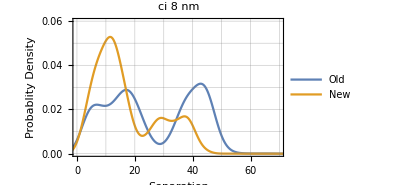
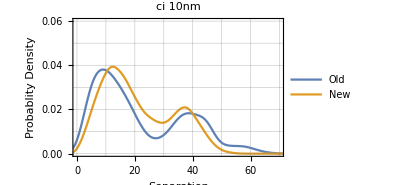

```mathematica
Row[Show[#,ImageSize -> imgSize]&/@
{
ListLinePlot[
Import[prefix<>#, "table", FieldSeparators ->" "]&/@{
"L680N_MBCD_EGF.old.ci_8.txt",
"L680N_MBCD_EGF.new.ci_8.txt"
},
PlotLegends->Placed[{"Old", "New"},Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"ci 8 nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}],
ListLinePlot[
Import[prefix<>#, "table", FieldSeparators ->" "]&/@{
"L680N_MBCD_EGF.old.ci_10.txt", 
"L680N_MBCD_EGF.new.ci_10.txt"
},
 PlotLegends->Placed[{"Old", "New"}, Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"ci 10nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}]
}]
```

The plots below show the probability density of separations for tracks accepted by the new filter, but rejected by the old filter (New \ Old) and tracks accepted by the old filter and rejected by the new filter (Old \ New) for 8nm and 10nm.

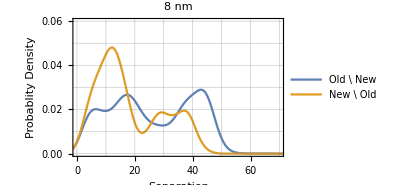
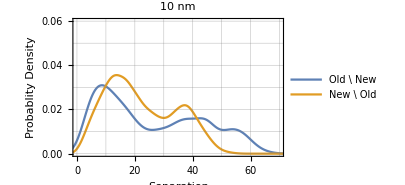

```mathematica
Row[Show[#,ImageSize-> imgSize]&/@{
ListLinePlot[
Import[prefix <> #, "table", FieldSeparators-> " "]&/@{
"L680N_MBCD_EGF.old-new.ci_8.txt",
"L680N_MBCD_EGF.new-old.ci_8.txt"
},
 PlotLegends->Placed[{"Old \\ New", "New \\ Old"},Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"8 nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}],
ListLinePlot[
Import[prefix <> #, "table", FieldSeparators-> " "]&/@{
"L680N_MBCD_EGF.old-new.ci_10.txt",
"L680N_MBCD_EGF.new-old.ci_10.txt"
}, 
 PlotLegends->Placed[{"Old \\ New", "New \\ Old"},Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"10 nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}]
}]
```

### Comparing the results from I942E EGFR Affibody

The new filter was used to select tracks from 390 data sets taken with the condition I942E EGFR Affibody and the tracks were analysed with FLImP. The results were compared with tracks selected from the same data sets with the old filter.

| Shown | Selected | <10nm | <8nm | <7nm
Old Filter | 14370 | 231 | 101 | 64 | 46
New Filter | 313 | 214 | 116 | 69 | 40

The plots below show the probability density of separation for tracks selected with the old and the new filter with confidence interval less than 8 nm and 10 nm and separation less than 60 nm.

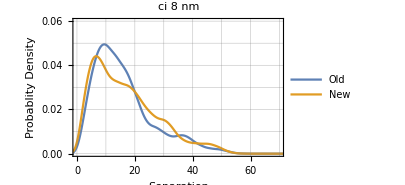
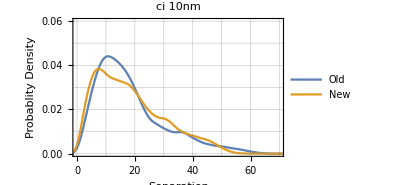

```mathematica
Row[Show[#,ImageSize -> imgSize]&/@
{
ListLinePlot[
Import[prefix<>#, "table", FieldSeparators ->" "]&/@{
"I942E.old.ci_8.txt",
"I942E.new.ci_8.txt"
},
PlotLegends->Placed[{"Old", "New"},Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"ci 8 nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}],
ListLinePlot[
Import[prefix<>#, "table", FieldSeparators ->" "]&/@{
"I942E.old.ci_10.txt", 
"I942E.new.ci_10.txt"
},
 PlotLegends->Placed[{"Old", "New"}, Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"ci 10nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}]
}]
```

The plots below show the probability density of separations for tracks accepted by the new filter, but rejected by the old filter (New \ Old) and tracks accepted by the old filter and rejected by the new filter (Old \ New) for 8 nm and 10 nm.

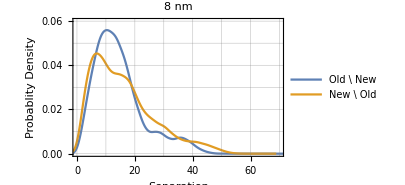
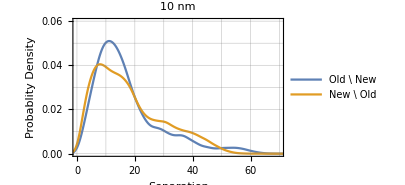

```mathematica
Row[Show[#,ImageSize-> imgSize]&/@{
ListLinePlot[
Import[prefix <> #, "table", FieldSeparators-> " "]&/@{
"I942E.old-new.ci_8.txt",
"I942E.new-old.ci_8.txt"
},
 PlotLegends->Placed[{"Old \\ New", "New \\ Old"},Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"8 nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}],
ListLinePlot[
Import[prefix <> #, "table", FieldSeparators-> " "]&/@{
"I942E.old-new.ci_10.txt",
"I942E.new-old.ci_10.txt"
}, 
 PlotLegends->Placed[{"Old \\ New", "New \\ Old"},Above], PlotRange->{{0, 70}, {0, 0.06}}, Ticks->ticks, GridLines->ticks, PlotLabel->"10 nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}]
}]
```

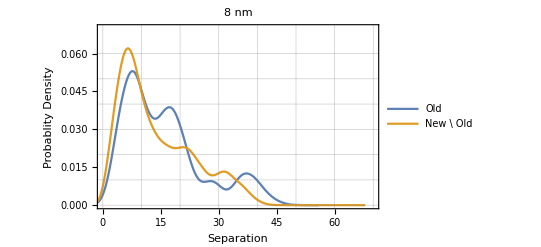

```mathematica
ListLinePlot[Import[prefix <>#,"table", FieldSeparators-> " "] &/@{
"I942E.old.dist_gt_60.ci_gt_6.18_tracks_density.txt",
"I942E.new.dist_gt_60.ci_gt_6.19_tracks_density.txt"
},
PlotLegends->Placed[{"Old", "New \\ Old"},Above], 
PlotRange->{{0, 70}, {0, 0.07}}, Ticks->ticks, GridLines->ticks, PlotLabel->"8 nm", Frame -> True, FrameLabel->{"Separation", "Probablity Density"}]
```